## General Setup

```mathematica
$Assumptions={r>0, R>0, γ>0,γR>0,γθ>0,Ts∈Reals, μ>0, A>0, B>0, σ≠ 0, MR≠0, Mθ≠0, Jg>0};
```

```mathematica
sol=Last@DSolve[{r'[R]==(R γR γθ)/r[R],TRR'[R]==(μ γR)/(R γθ) (1-(R^4 γθ^4)/r[R]^4),r[0]==0,TRR[B]==0},{r[R],TRR[R]},R]//FullSimplify
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -2 1 == 0.

{r[R]→R √(γR γθ),TRR[R]→((-γR^2+γθ^2) μ Log[B/R])/(γR γθ)}

```mathematica
TRRanalytical[R_]:=((-γR^2+γθ^2) μ Log[B/R])/(γR γθ)
```

```mathematica
TRR[R]+(μ r[R]^2)/(R^2 γθ^2)(1-(R^4 γθ^4)/r[R]^4)/.sol
```

(γR (1-γθ^2/γR^2) μ)/γθ+((-γR^2+γθ^2) μ Log[B/R])/(γR γθ)

```mathematica
Tθθanalytical[R_]:=(γR (1-γθ^2/γR^2) μ)/γθ+((-γR^2+γθ^2) μ Log[B/R])/(γR γθ)
```

```mathematica
TRRanalytical[R]-Tθθanalytical[R]/.sol//FullSimplify
```

-(γR μ)/γθ+(γθ μ)/γR

```mathematica
RHSR:=  ReplaceAll[γR  KR (TRRanalytical[R]-Tθθanalytical[R]-Ts)-S γR^2,{γR->γR[t], γθ->γθ[t]}]//FullSimplify
RHSθ:=  ReplaceAll[ γθ Kθ(TRRanalytical[R]-Tθθanalytical[R]-Ts)-S γθ^2,{γR->γR[t], γθ->γθ[t]}]//FullSimplify
```

```mathematica
RHSR
```

-KR Ts γR[t]+KR μ γθ[t]-(γR[t]^2 (KR μ+S γθ[t]))/γθ[t]

```mathematica
RHSθ
```

-Kθ μ γR[t]+(Kθ μ γθ[t]^2)/γR[t]-γθ[t] (Kθ Ts+S γθ[t])

```mathematica
γanalytical=γR[t]/.First@DSolve[{γR'[t]==ReplaceAll[RHSR, {S->0, γθ[t]->1}], γR[0]==1},γR[t],t]//FullSimplify;
```

```mathematica
(* domain size *)
```

```mathematica
B √γanalytical//FullSimplify
```

(B √((-Ts+√(Ts^2+4 μ^2) Tanh[1/2 KR t √(Ts^2+4 μ^2)+ArcTanh[(Ts+2 μ)/(√(Ts^2+4 μ^2))]])/μ))/(√2)

```mathematica
(* Limit[B √γanalytical, t->∞] *)
```

```mathematica
WartlickRadii={{24.,6.33},{36.,8.94},{48.,23.79},{60.,47.47},{73.,59.76},{84.,77.87},{96.,89.41}};
```

```mathematica
temp=Last@Solve[{0==RHSR,0==RHSθ}/.S->0,{γR[t], γθ[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{γθ[t]→(Ts γR[t]+√(Ts^2+4 μ^2) γR[t])/(2 μ)}

```mathematica
{0==RHSR}/.S->0/.Kθ->0
```

{0==-KR Ts γR[t]-(KR μ γR[t]^2)/γθ[t]+KR μ γθ[t]}

```mathematica
RHSR
```

-KR Ts γR[t]+KR μ γθ[t]-(γR[t]^2 (KR μ+S γθ[t]))/γθ[t]

```mathematica
2 √(γR[t]γθ[t])/.temp//FullSimplify
```

√2 √(((Ts+√(Ts^2+4 μ^2)) γR[t]^2)/μ)

## Deviatoric stress

```mathematica
stress = devStress + hydrStress
```

devStress+hydrStress

```mathematica
deviatoric[tensor_]:=tensor-1/2 Tr[tensor] IdentityMatrix[2]
hydrostatic[tensor_]:=1/2 Tr[tensor] IdentityMatrix[2]
```

```mathematica
stressTensor[R_]:=DiagonalMatrix@{TRRanalytical[R],Tθθanalytical[R]}
```

```mathematica
deviatoric@stressTensor[R]//FullSimplify
```

{{-(γR μ)/(2 γθ)+(γθ μ)/(2 γR),0},{0,((γR-γθ) (γR+γθ) μ)/(2 γR γθ)}}

```mathematica
%==μ/2 (γθ/γR-γR/γθ){{1, 0},{0, -1}}
```

True

{{-((γR-γθ) (γR+γθ) μ (-1+2 Log[B/R]))/(2 γR γθ),0},{0,-((γR-γθ) (γR+γθ) μ (-1+2 Log[B/R]))/(2 γR γθ)}}

```mathematica
hydrostatic@stressTensor[R]//FullSimplify
%==-μ/2 (γθ/γR-γR/γθ)(1+2 Log[R/B])IdentityMatrix[2]//FullSimplify
```

{{-((γR-γθ) (γR+γθ) μ (-1+2 Log[B/R]))/(2 γR γθ),0},{0,-((γR-γθ) (γR+γθ) μ (-1+2 Log[B/R]))/(2 γR γθ)}}

True

```mathematica
stressTensor[R]-(deviatoric@stressTensor[R]+hydrostatic@stressTensor[R])//FullSimplify
```

{{0,0},{0,0}}

```mathematica
deviatoric[stressTensor''[R]]//FullSimplify
```

{{0,0},{0,0}}

```mathematica
stressTensor'[R]
```

{{-((-γR^2+γθ^2) μ)/(R γR γθ),0},{0,-((-γR^2+γθ^2) μ)/(R γR γθ)}}

```mathematica
deviatoric@{{a,0},{ 0, b}}//FullSimplify
```

{{(a-b)/2,0},{0,1/2 (-a+b)}}

```mathematica
D[TRRanalytical[R],R]
```

-((-γR^2+γθ^2) μ)/(R γR γθ)

```mathematica
deviatoric[stressTensor[R]^(1/2)]//FullSimplify
```

{{1/2 (√(((-γR^2+γθ^2) μ Log[B/R])/(γR γθ))-√(((γR-γθ) (γR+γθ) μ (1-Log[B]+Log[R]))/(γR γθ))),0},{0,1/2 (-√(((-γR^2+γθ^2) μ Log[B/R])/(γR γθ))+√(((γR-γθ) (γR+γθ) μ (1-Log[B]+Log[R]))/(γR γθ)))}}

## Some functional explorations

```mathematica
Limit[γanalytical, t->∞]
```

ConditionalExpression[(-Ts+√(Ts^2+4 μ^2))/(2 μ),ArcTanh[(Ts+2 μ)/(√(Ts^2+4 μ^2))]∈ℝ&&KR>0]

```mathematica
FitParameters={KR-> 5.01*10^-6, Ts->-2.09*10^4, μ->10,B->2.0 };
```

```mathematica
γanalytical
```

(-Ts+√(Ts^2+4 μ^2) Tanh[1/2 KR t √(Ts^2+4 μ^2)+ArcTanh[(Ts+2 μ)/(√(Ts^2+4 μ^2))]])/(2 μ)

```mathematica
{TRRanalytical[R],Tθθanalytical[R]}.{Cos[θ], Sin[θ]}/.FitParameters/.R->2
```

0.+(0.+(10 γR (1-γθ^2/γR^2))/γθ) Sin[θ]

```mathematica
(Ts+2 μ)/(√(Ts^2+4 μ^2))/.FitParameters
```

-0.999043

```mathematica
γanalytical/.FitParameters
```

1/20 (20900.-20900. Tanh[3.82198-0.0523545 t])

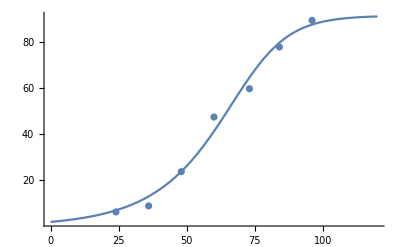

```mathematica
LP=ListPlot[WartlickRadii];
PP=Plot[2 √γanalytical/.FitParameters//Evaluate, {t, 0, 120}, PlotRange->All];
Show[PP, LP]
```

```mathematica
γInterp=Interpolation[Table[{time, γanalytical/.FitParameters/.t->time}, {time, 0, 120}]]
```

InterpolatingFunction[…]

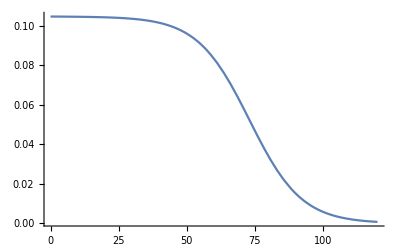

```mathematica
Plot[γInterp'[t]/γInterp[t], {t, 0, 120}, PlotRange->All]
```

```mathematica
subt=First@Solve[1/2 KR t √(Ts^2+4 μ^2)+ArcTanh[(Ts+2 μ)/(√(Ts^2+4 μ^2))]==0, t]//FullSimplify
```

{t→-(2 ArcTanh[(Ts+2 μ)/(√(Ts^2+4 μ^2))])/(KR √(Ts^2+4 μ^2))}

```mathematica
subt/.FitParameters
```

{t→73.0019}

```mathematica
temp=-γanalytical μ+μ/γanalytical/.subt//FullSimplify
```

Ts/2-(2 μ^2)/Ts

```mathematica
2/Ts temp//FullSimplify
```

1-(4 μ^2)/Ts^2

```mathematica
D[γanalytical, t]/.subt//FullSimplify
```

KR (Ts^2/(4 μ)+μ)

## Finding the right parameters

```mathematica
tend=500 (* hours *);
tplot=120;

μ=10 (* INITIAL STIFFNESS OF THE TISSUE kPa *);
B=2; (* μm *)
solNumerical[{KR_,Kθ_, Ts_,S_},{ γR0_, γθ0_}]:=Module[{},
First@NDSolve[{
γR'[t]==-KR Ts γR[t]+KR μ γθ[t]-(γR[t]^2 (KR μ+S γθ[t]))/γθ[t], 
γθ'[t]==-Kθ μ γR[t]+(Kθ μ γθ[t]^2)/γR[t]-γθ[t] (Kθ Ts+S γθ[t]),

γR[0]==γR0, γθ[0]==γθ0},{γR[t], γθ[t]},{t, 0, tend}]]
```

```mathematica
stringify[x_]:=ToString[ScientificForm[x//N], StandardForm]
Manipulate[
LP=ListPlot[WartlickRadii];
tab="\n";
stringKR="K_R = "<>stringify[10^Log10factor];
stringKθ="K_θ = "<>stringify[10^Log10factor KθoverKR];
stringTs="T^* = "<>stringify[-10^Log10Ts];
stringS="S = "<>stringify[10^Log10S];
stringγ="(γR, γθ) = "<>stringify[p];
labelString=stringKR<>tab<>stringKθ<>tab<>stringTs<>tab<>stringS<>tab<>stringγ;
solCurrent=solNumerical[{10^Log10factor (* kPa^-1 hours^-1 *),KθoverKR 10^Log10factor(* kPa^-1 hours^-1 *), -10^Log10Ts (* kPa *),10^Log10S (* unit? *) },p]//Quiet;
PP=Plot[{2 (* μm *) √(γR[t]γθ[t]),γR[t]/γθ[t]}/.solCurrent//Evaluate,{t, 0,  tplot}, PlotRange->{{0, tplot},{0, 150}}, PlotLabel->labelString, ImageSize->400];

PhasePlot=ParametricPlot[{γR[t],γθ[t]}/.solCurrent//Evaluate//Quiet,{t, 0, tend}, ImageSize->400, PlotRange->range{{0.001,1}, {0.001,1}}];
range=200;
CP=ContourPlot[100==2 √(γR[t]γθ[t]),{γR[t], 0, range}, {γθ[t], 0, range}, ContourStyle->Directive[Black, Dashed]];
(* SP=StreamPlot[{RHSR,RHSθ}/.{KR-> 10^Log10factor, Kθ->KθoverKR 10^Log10factor, Ts-> -10^Log10Ts, S->10^Log10S}//Evaluate,{γR[t], 0.001, range}, {γθ[t], 0.001, range} ]; *)
Grid[{{Show[PP, LP],Show[ PhasePlot, CP(*, SP*)]}}],
{{KθoverKR, 0.8333},0, 5}, 
{{Log10factor, -2.7608}, -8,0},
{{Log10Ts, 1.68}, 1, 6},
{{Log10S, -2.85}, -4, 4},
{{p,{1,1}},Locator},
Row[{
Button["one DOF model",KθoverKR=0;Log10factor=-5.39; Log10Ts= 4.4;Log10S=-15;  p={1,1},ImageSize->150],
Button["OLD one DOF model",KθoverKR=0;Log10factor=-5.3; Log10Ts= 4.32;Log10S=-15;  p={1,1},ImageSize->150],
Button["No Size Control Fit",KθoverKR=0.55;Log10factor=-3.022; Log10Ts=Log10[ 10*μ ];Log10S=-15;  p={1,1},ImageSize->150],
Button["Size Control Fit",KθoverKR=0.8333;Log10factor=-2.7608; Log10Ts=1.68;Log10S=-2.85;  p={1,1},ImageSize->150]}]
]
```

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{0.001 range,range},{0.001 range,range}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{0.001 range,range},{0.001 range,range}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in K_R = <>stringify[0.0017346].

StringJoin::string: String expected at position 2 in K_θ = <>stringify[0.00144544].

StringJoin::string: String expected at position 2 in T^* = <>stringify[-47.863].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{0.001 range,range},{0.001 range,range}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{0.001 range,range},{0.001 range,range}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
FitParameters={μK->10^-4.30,  Ts->-10^3.32,BγR->2 }
```

{μK→0.0000501187,Ts→-2089.3,BγR→2}

## No size control 2D model

```mathematica
sol1=solNumerical[{9.51 10^-4 (* kPa^-1 hours^-1 *),5.22 10^-4(* kPa^-1 hours^-1 *),-10^2 (* kPa *),0 (* unit? *) },{1,1}]//Quiet;
sol2=solNumerical[{9.51 10^-4 (* kPa^-1 hours^-1 *),5.22 10^-4(* kPa^-1 hours^-1 *),-10^2 (* kPa *),0 (* unit? *) },{1.54,0.8}]//Quiet;
sol3=solNumerical[{9.51 10^-4 (* kPa^-1 hours^-1 *),5.22 10^-4(* kPa^-1 hours^-1 *),-10^2 (* kPa *),0 (* unit? *) },{0.93,1.14}]//Quiet;
solArray={sol1, sol2, sol3};
```

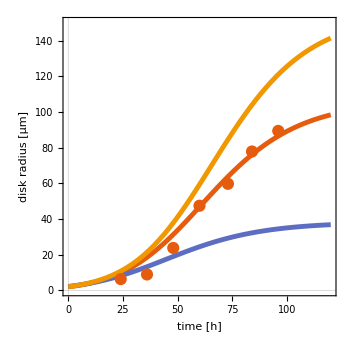
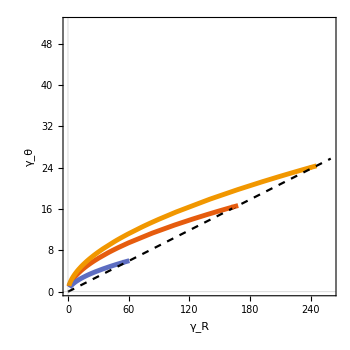

```mathematica
LP=ListPlot[WartlickRadii, PlotTheme->"Scientific", PlotStyle->PointSize[0.025]];
SP=StreamPlot[{RHSR,RHSθ}/.{KR-> 9.51 10^-4, Kθ->5.22 10^-4, Ts-> -10^2 , S->0}//Evaluate,{γR[t], 0.001, range}, {γθ[t], 0.001, range} , StreamPoints->Fine, StreamStyle->Lighter@Gray];

range=260;
th=0.01;
is=350;
PP=Plot[2 (* μm *) √(γR[t]γθ[t])/.#&/@solArray//Evaluate,{t, 0,  tplot}, PlotRange->{{0, tplot},{0, 150}},  ImageSize->is, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->25, FrameStyle->Black, PlotStyle->Thickness[th], FrameLabel->{"time [h]", "disk radius [μm]"}];
CP=Plot[(Ts γR[t]+√(Ts^2+4 μ^2) γR[t])/(2 μ)/.{Ts->-10^2},{γR[t],  0.001, range}, PlotStyle->Directive[Black, Dashed]];
PhasePlot=ParametricPlot[{γR[t],γθ[t]}/.#&/@solArray//Evaluate,{t, 0, tend}, ImageSize->is, PlotRange->range{{0.001,1}, {0.001,0.2}}, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->25, FrameStyle->Black, PlotStyle->Thickness[th], FrameLabel->{"γ_R", "γ_θ"}]/.Line[x_]:>{Arrowheads[0.8{0.,0.07,0.07,0.}],Arrow[x]};
G1={Show[PP, LP],Show[ PhasePlot,   CP]}
```

```mathematica
sol1=solNumerical[{1.73 10^-3 (* kPa^-1 hours^-1 *),1.45 10^-3  (* kPa^-1 hours^-1 *),-4.79 10^1 (* kPa *),1.41 10^-3 (* unit? *) },{1,1}]//Quiet;
sol2=solNumerical[{1.73 10^-3 (* kPa^-1 hours^-1 *),1.45 10^-3  (* kPa^-1 hours^-1 *),-4.79 10^1 (* kPa *),1.41 10^-3 (* unit? *) },{6.2,2.2}/1.5]//Quiet;
sol3=solNumerical[{1.73 10^-3 (* kPa^-1 hours^-1 *),1.45 10^-3  (* kPa^-1 hours^-1 *),-4.79 10^1 (* kPa *),1.41 10^-3 (* unit? *) },{2.5,6.6}/1.5]//Quiet;

solArray={sol1, sol2, sol3};
```

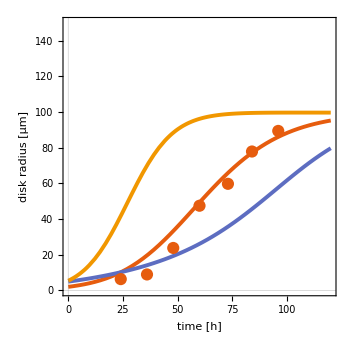
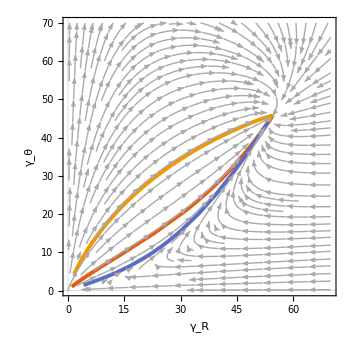

```mathematica
range=70;

LP=ListPlot[WartlickRadii, PlotTheme->"Scientific", PlotStyle->PointSize[0.025]];
SP=StreamPlot[{RHSR,RHSθ}/.{KR-> 1.73 10^-3, Kθ->1.45 10^-3, Ts-> -4.79 10^1 , S->1.41 10^-3}//Evaluate,{γR[t], 0.001, range}, {γθ[t], 0.001, range} , StreamPoints->Fine, StreamStyle->Lighter@Gray];


th=0.008;
is=350;
PP=Plot[2 (* μm *) √(γR[t]γθ[t])/.#&/@solArray//Evaluate,{t, 0,  tplot}, PlotRange->{{0, tplot},{0, 150}},  ImageSize->is, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->25, FrameStyle->Black, PlotStyle->Thickness[th], FrameLabel->{"time [h]", "disk radius [μm]"}];
PhasePlot=ParametricPlot[{γR[t],γθ[t]}/.#&/@solArray//Evaluate,{t, 0, tend}, ImageSize->is, PlotRange->range{{0.001,1}, {0.001,1}}, PlotTheme->"Scientific", AspectRatio->1, BaseStyle->25, FrameStyle->Black, PlotStyle->Thickness[th], FrameLabel->{"γ_R", "γ_θ"}]/.Line[x_]:>{Arrowheads[0.8{0.,0.07,0.07,0.}],Arrow[x]};
G2={Show[PP, LP],Show[ PhasePlot,   SP]}
```

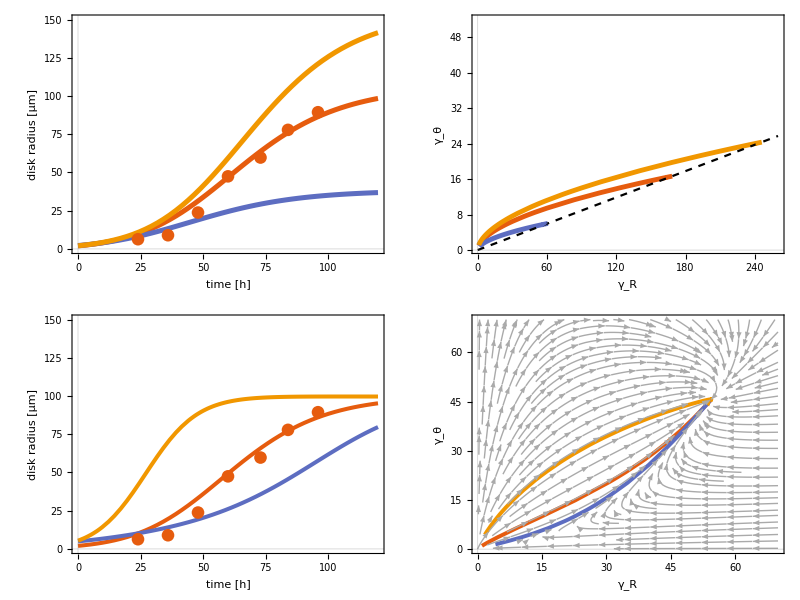

```mathematica
Grid[{G1, G2}]
```

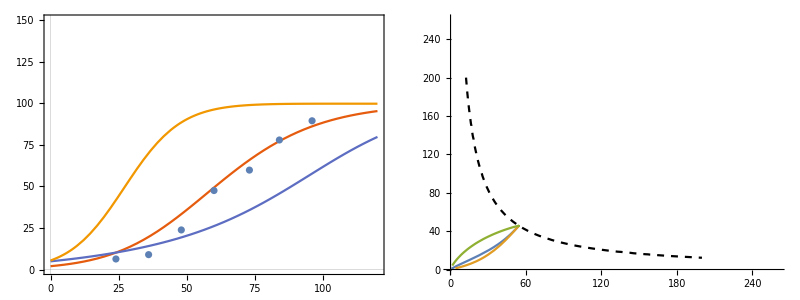

```mathematica
range=260;
tplot=120;
PP=Plot[2 (* μm *) √(γR[t]γθ[t])/.#&/@solArray//Evaluate,{t, 0,  tplot}, PlotRange->{{0, tplot},{0, 150}},  ImageSize->400, PlotTheme->"Scientific"];
PhasePlot=ParametricPlot[{γR[t],γθ[t]}/.#&/@solArray//Evaluate,{t, 0, tend}, ImageSize->400, PlotRange->range{{0.001,1}, {0.001,1}}];
Grid[{{Show[PP, LP],Show[ PhasePlot, CP(*, SP*)]}}]
```